```mathematica
With[
{all=allGraphs4},
Select[Keys[all],Length[ListofVars[all[#,"colofour"]]]==Length[ListofVars[all[#,"colofourrealnull"]]]&]
]
```

{728}

```mathematica
allGraphs4[728,"graph"]
```

-Graphics-

```mathematica
With[
{all=allGraphs5},
Select[Keys[all],Length[ListofVars[all[#,"colofour"]]]==Length[ListofVars[all[#,"colofourrealnull"]]]&]
]
```

{59048}

```mathematica
allGraphs5[59048,"graph"]
```

-Graphics-

```mathematica
With[
{all=allGraphs6},
Select[Keys[all],Length[ListofVars[all[#,"colofour"]]]==Length[ListofVars[all[#,"colofourrealnull"]]]&]
]
```

{14348906}

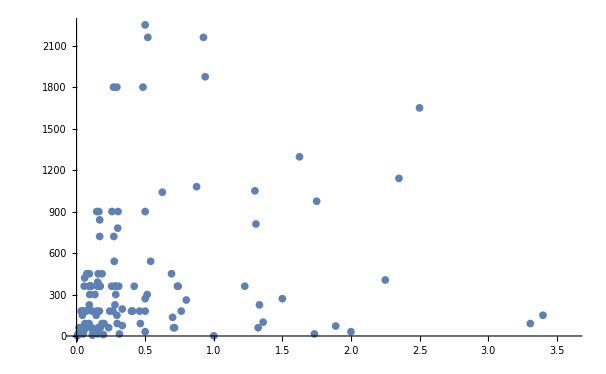

```mathematica
With[
{all=allGraphs6},
Map[{#[[1,1]]/#[[1,2]],#[[2]]}&,Sort[Tally[Table[{Length[ListofVars[all[k,"colofour"]]],Length[ListofVars[all[k,"colofourrealnull"]]]},{k,Keys[all]}]]]]
]//ListPlot
```

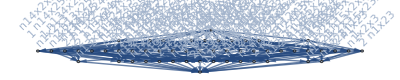

```mathematica
g=MobiusGraph4[k5Key,allGraphs5]
```

{IsRefinement,{{1,2},{3,4,6},{5}},{{1},{2},{3,4,6},{5}}}

{IsRefinement,{{1,3,4,6},{2},{5}},{{1},{2},{3,4,6},{5}}}

{IsRefinement,{{1,5},{2},{3,4,6}},{{1},{2},{3,4,6},{5}}}

{IsRefinement,{{1},{2,3,4,6},{5}},{{1},{2},{3,4,6},{5}}}

{IsRefinement,{{1},{2,5},{3,4,6}},{{1},{2},{3,4,6},{5}}}

{IsRefinement,{{1},{2},{3,4,5,6}},{{1},{2},{3,4,6},{5}}}

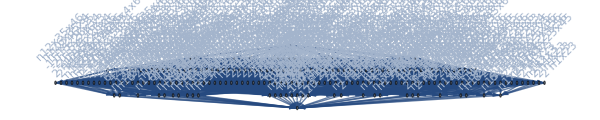

```mathematica
g=MobiusGraph4[K6Key,allGraphs6]
```

```mathematica
Table[{StringCount[SymbolName[v],"x"], VertexOutDegree[g,v]},{v,VertexList[g]}]//Tally//Sort
```

{{{0,0},1},{{1,1},31},{{2,3},90},{{3,6},65},{{4,10},15},{{5,15},1}}

```mathematica
Select[Table[{StringCount[SymbolName[v],"x"], v,VertexOutDegree[g,v]},{v,VertexList[g]}],#[[1]]==4&]
```

{{4,n12x3x4x5x6,10},{4,n13x2x4x5x6,10},{4,n14x2x3x5x6,10},{4,n15x2x3x4x6,10},{4,n16x2x3x4x5,10},{4,n1x23x4x5x6,10},{4,n1x24x3x5x6,10},{4,n1x25x3x4x6,10},{4,n1x26x3x4x5,10},{4,n1x2x34x5x6,10},{4,n1x2x35x4x6,10},{4,n1x2x36x4x5,10},{4,n1x2x3x45x6,10},{4,n1x2x3x46x5,10},{4,n1x2x3x4x56,10}}

```mathematica
Select[EdgeList[g],#[[1]]==n1x2x346x5&]
```

{n1x2x346x5->n12x346x5,n1x2x346x5->n1346x2x5,n1x2x346x5->n15x2x346,n1x2x346x5->n1x2346x5,n1x2x346x5->n1x25x346,n1x2x346x5->n1x2x3456}

```mathematica
Table[StirlingS2[6,k],{k,1,6}]
```

{1,31,90,65,15,1}

```mathematica
Table[VertexOutDegree[g,v],{v,VertexList[g]}]//Tally//Sort//TableForm
```

0 | 1
1 | 31
3 | 90
6 | 65
10 | 15
15 | 1

```mathematica
Table[StirlingS2[5,n],{n,1,5}]
```

{1,15,25,10,1}

```mathematica
allGraphs4[0,"vertexsets"]
```

{{1},{2},{3},{4}}